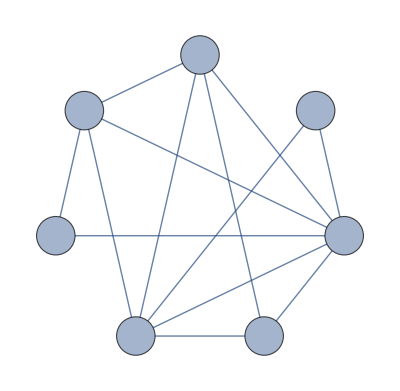

(-1 | -1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | -1 | -1 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | -1 | -1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | -1)

```mathematica
inFileName=StringJoin[{NotebookDirectory[],"input.txt"}];
fileStream=OpenRead[inFileName];
vertex=Read[fileStream, {Word,Number}][[2]];
edge=Read[fileStream, {Word,Number}][[2]];
edges=ReadList[fileStream,Expression,edge];
array=Array[0&,vertex];
listInput=ReadList[fileStream,String];
For[i=1,i≤vertex,i++,array[[i]]=ToExpression[StringSplit[listInput[[i]],{"b","_","/*","*/"}]][[2]]];
verticesList=Array[#&,vertex];
edgesList=Table[edges[[i,1]]-> edges[[i,2]],{i,edge}];
Close[fileStream];
graph=Graph[verticesList,edgesList, GraphLayout->"CircularEmbedding", VertexSize->0.3, VertexLabels->Placed["Name", Center], VertexLabelStyle->Directive[Bold,Italic,20],EdgeShapeFunction->GraphElementData["Arrow","ArrowSize"->0.05]]
IncidenceMatrix[graph]//MatrixForm
```